```mathematica
DateString[]
$Version
```

Thu 26 Sep 2019 15:12:10

12.0.0 for Microsoft Windows (64-bit) (April 6, 2019)

## Lecture 07 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

### 39 Immediate and Delayed Values

39 Immediate and Delayed Values

```mathematica
value=RandomInteger[10]
```

8

```mathematica
value
```

8

```mathematica
value
```

10

```mathematica
value
```

7

```mathematica
value
```

7

```mathematica
value
```

10

```mathematica
value
```

4

```mathematica
value:=RandomInteger[10]
```

```mathematica
value
```

0

```mathematica
value
```

5

6

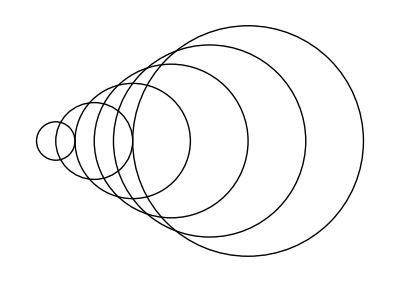

```mathematica
circles:=Graphics[Table[Circle[{x,0},x/2],{x,n}]]
n=6
circles
```

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.177338,0.177338,0.177338,0.177338}

```mathematica
x:>RandomReal[]
{x,x,x,x}/.x:>RandomReal[]
```

x:>RandomReal[]

{0.694903,0.244932,0.687474,0.755983}

Picky examples:

### 40 Defining Your Own Functions

40 Defining Your Own Functions

```mathematica
number[n_]:=Table[RandomInteger[10,n],n]
```

```mathematica
number[4]
```

{{1,0,7,2},{7,6,0,4},{7,2,0,10},{0,3,1,0}}

```mathematica
number[4]
```

{{8,0,3,4},{8,4,7,6},{5,4,2,9},{9,4,4,10}}

```mathematica
factorial[1]=1;factorial[n_Integer]:=n*factorial[n-1]
factorial[50]
50!
```

30414093201713378043612608166064768844377641568960512000000000000

30414093201713378043612608166064768844377641568960512000000000000

```mathematica
plusminus[{x_,y_}]:={x+y,x-y}
plusminus[{3,4}]
```

{7,-1}

```mathematica
plusminus[v_]:={v[[1]]+v[[2]],v[[1]]-v[[2]]}
plusminus[{3,4}]
```

{7,-1}

Discussion about upvalue

```mathematica
TagSetDelayed
```

Picky examples: 6

### 41 More about Patterns

41 More about Patterns

```mathematica
_ ("blank") stands for anything.x_ ("x blank") stands for anything,but calls it x._h stands for anything with head h.And x_h stands for anything with head h,and calls it x.
```

Picky examples: 1, 4, 5, 6

### 42 String Patterns and Templates

42 String Patterns and Templates

```mathematica
LocalObject[]
```

LocalObject[file:///C:/Users/admin/AppData/Roaming/Wolfram/Objects/4f1bfc40-a71d-4a97-b848-c5cf9aa2b23f]

```mathematica
Put[-Graphics-,%]
```

LocalObject[file:///C:/Users/admin/AppData/Roaming/Wolfram/Objects/4f1bfc40-a71d-4a97-b848-c5cf9aa2b23f]

```mathematica
Get[%]
```

-Graphics-

Picky examples: 3, 4, 5, 6, 7

### 43 Storing Things *

43 Storing Things

```mathematica
The Wolfram Language makes it easy to store things either in the Wolfram Cloud,or locally on your computer system.
```

Picky examples:

### 44 Importing and Exporting

44 Importing and Exporting

```mathematica
WebImageSearch["dog"]
```

Dataset[<>]

```mathematica
WebImageSearch["dog","Images"]
```

```mathematica
WebImageSearch["colorful birds","Thumbnails"]
```

```mathematica
SendMail["chwang@gist.ac.kr", {"Wolf", "Here's a wolf...", -Graphics-}]
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

Success[MailSent,<|MessageTemplate:>SendMail::success,Recipient→chwang@gist.ac.kr,MessageID→16234916049327295677.0.WolframLanguage.chwang@gist.ac.kr|>]

Picky examples: 1, 2, 4, 5, 7, 9

### 45 Datasets *

45 Datasets

Create a simple dataset that can be viewed as having 2 rows and 3 columns:

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

Get the element from “row b” and “column z”:

```mathematica
data["b","z"]
```

You can first extract the whole “b row”, then get the “z” element of the result:

```mathematica
data["b"]["z"]
```

Generate a new dataset from the “b row” of the original dataset:

```mathematica
data["b"]
```

Generate a dataset consisting of the “z column” for all rows:

```mathematica
data[All,"z"]
```

Get totals for each row by applying Total to all columns for all the rows:

```mathematica
data[All,Total]
```

Apply the function f to each row:

```mathematica
data[All,f]
```

Apply a function that adds the x and z elements of each association:

```mathematica
data[All,#x+#z&]
...
```

Picky examples: 1, 2, 3, 5, 7, 8, 10, 11, 12, 13

### 46 Writing Good Code *

46 Writing Good Code

```mathematica
fromdigits=Fold[{10,1}.{##}&,#]&;
```

```mathematica
fromdigits[{5,6,1,7,8}]
```

56178

```mathematica
FromDigits[{5,6,1,7,8}]
```

56178

Doctrines of Writing a Good Code

Draw a big picture what this you try to do.

Make it simple.

Give a proper name.

Use a function what does exactly what you want.

10 Tips for Writing Fast Mathematica Code

Picky examples:

### 47 Debugging Your Code *

47 Debugging Your Code

```mathematica
Graphics[{Circle[{0,0}],Disk[{a,b}]}]
```

-Graphics-

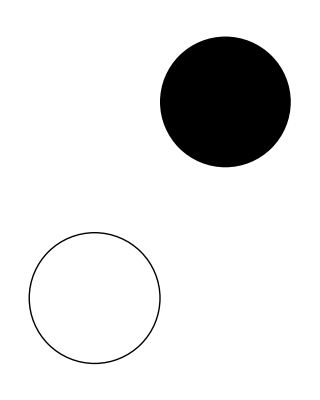

```mathematica
Graphics[{Circle[{0,0}],Disk[{2,3}]}]
```

```mathematica
Table[PrimeQ[2^2^n+1],{n,15}]
```

{True,True,True,True,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Monitor[Table[PrimeQ[2^2^n+1],{n,15}],Framed[n]]
```

{True,True,True,True,False,False,False,False,False,False,False,False,False,False,False}

Wolfram Workbench: IDE for the Wolfram Language

Picky examples: 1, 3

### What We Haven’t Discussed *

What We Haven’t Discussed

User Interface Construction

Function Visualization

Mathematical Computation

Numerics

Geometry

Algorithms

Logic

The Computational Universe

...

### Afterword: Being a Programmer *

Afterword: Being a Programmer